## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="FBA2";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;

(* user will need to change this path *)
pathMASSef = "/home/mrama/Dropbox/test bla/MASSef/";
kineticDataFileName =  "kinetic_data_model.csv";

mainFolder = "fit";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Working dir:/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00076 | 0.000722
0.000798 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00019 | 0.00016
0.00022 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00024 | 0.00021
0.00027 |  | M | 8 | 30 | trishcl | 0.05 | 
1 | fdp | 0.00085 | 0.0008075
0.0008925 |  | M | 7.5 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 8.17 | 7.73
8.6 | 1/s | 8 | 30 | trishcl | 0.05 | 
1 | fdp | Null | 10.33 | 10.03
10.63 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kic | dhap | 9.×10^-6 | 7.8×10^-6
0.0000102 |  | Competitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.000118 | 0.000095
0.000141 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.000221 | 0.000194
0.000248 |  | NonCompetitive | fdp | 0.00019 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority (optional)

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,0,0,0};
s05Priorities = Null;
kcatPriorities = {1,0,0};
inhibitionPriorities={1,1,1,0,0,0};
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

Ordered Sequential Uni Bi; [fdp,g3p,dhap]

Structure: 2

Active sites: 2

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp,Null | 0.00076 | 0.000722
0.000798 | Null | Null | 7 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | 0.00017 | 0.000167
0.000173 |  | M | 8 | 30 | trishcl | 0.05 |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | fdp | Null | 10.5 | 9.83
11.2 | 1/s | 8 | 30 | trishcl | 0.05 |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | Kic | dhap | 0.00013 | 0.000119
0.000141 |  | Competitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincc | g3p | 0.00003 | 0.000025
0.000035 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 | 
1 | Kincu | g3p | 0.00023 | 0.000188
0.000272 |  | NonCompetitive | fdp | 0.00017 | M | 8 | 30 | trishcl | 0.05 |

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Construct Module and Set Up Comparison Equations

### Construct enzyme module

```mathematica
rxn
```

(fdp^c⇌dhap^c+g3p^c)^FBA2

```mathematica
catalyticBranch={"E_FBA2[c] + fdp[c] <=> E_FBA2[c]&fdp",
				"E_FBA2[c]&fdp <=> E_FBA2[c]&dhap&g3p",
				"E_FBA2[c]&dhap&g3p <=> E_FBA2[c]&dhap + g3p[c]",
				"E_FBA2[c]&dhap <=> E_FBA2[c] + dhap[c]"};

enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,((FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c)^FBA22,((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,((FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c)^FBA24}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((FBA2^c)_^+fdp^c⇌(FBA2^c&fdp^c)_^)^FBA21,Overscript[(FBA2^c&dhap^c)_^⇌(FBA2^c)_^+dhap^c, FBA22],((FBA2^c&fdp^c)_^⇌(FBA2^c&dhap^c&g3p^c)_^)^FBA23,Overscript[(FBA2^c&dhap^c&g3p^c)_^⇌(FBA2^c&dhap^c)_^+g3p^c, FBA24]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

### Setup King-Altman Equations

```mathematica
MWCFlag=False;
nActiveSites=1;
simplifyMaxTime=300;
otherMetsReverseZeroSub={{"prod_inhib_dhap",m["g3p","c"]->0}, {"prod_inhib_g3p",m["dhap","c"]->0}};
 otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpFluxEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList,inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyMaxTime, nActiveSites];
```

kcat for

kcat rev

km for

km rev

## Semi-Automated Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={};
```

### Simulate data without uncertainty

```mathematica
fileList
```

{/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateRev.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateRev_dhap.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateRev_g3p.txt,/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt}

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList
, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.0144975}

```mathematica
FilePrint@dataPathList
```

Priority	dhap[c]	fdp[c]	g3p[c]	param_FBA2_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0	0	1	7	25	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt"	0.00076
1	0	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.09090909090909094
1	0	0.00002694318427183895	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.1368068886032101
1	0	0.000042702069335662915	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.20076000891310194
1	0	0.0000676782189940945	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.28474724895080133
1	0	0.00010726274856163285	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.386863179846857
1	0	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.5000000000000001
1	0	0.0002694318427183895	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.6131368201531432
1	0	0.0004270206933566291	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.7152527510491988
1	0	0.0006767821899409458	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.7992399910868985
1	0	0.0010726274856163284	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.86319311139679
1	0	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt"	0.9090909090909091
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0	0.01	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt"	10.5
1	0.000065	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.06250000000000003
1	0.000065	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.17411239489546837
1	0.000065	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.4000000000000001
1	0.000065	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.6782688399674106
1	0.000065	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.8695652173913043
1	0.00013	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.04761904761904764
1	0.00013	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.13652705949581437
1	0.00013	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.3333333333333335
1	0.00013	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.6125741132772069
1	0.00013	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.8333333333333333
1	0.00026	0.000017000000000000007	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.032258064516129045
1	0.00026	0.00005375872022286247	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.09535767393826002
1	0.00026	0.00017000000000000007	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.2500000000000001
1	0.00026	0.0005375872022286248	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.5131670194948621
1	0.00026	0.0017000000000000008	0	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt"	0.7692307692307693
1	0	0.000017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.030349681108423142
1	0	0.00005375872022286247	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.08852308825306443
1	0	0.00017000000000000007	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.22475570032573297
1	0	0.0005375872022286248	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.43782901894103
1	0	0.0017000000000000008	0.00006500000000000001	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.6252831898504759
1	0	0.000017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.01821541710665259
1	0	0.00005375872022286247	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.05425730412803112
1	0	0.00017000000000000007	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.14495798319327732
1	0	0.0005375872022286248	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.3075252527148365
1	0	0.0017000000000000008	0.00013000000000000002	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.4765193370165746
1	0	0.000017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.010121754437435824
1	0	0.00005375872022286247	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.030581863846891433
1	0	0.00017000000000000007	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.08476658476658477
1	0	0.0005375872022286248	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.1927783983056278
1	0	0.0017000000000000008	0.00026000000000000003	1	8	30	"/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt"	0.32288254562470753

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«7 more identical outputs»

```mathematica
FilePrint[dataPathList[[1]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	0.3976299557399333
0	0.089	3.8624414067610525e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	6.1215570918555205e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.1368068886032101
0	0.089	9.702014162143871e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310197
0	0.089	0.00001537665619874311	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.2847472489508014
0	0.089	0.000024370357732202946	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.38686317984685703
0	0.089	0.00003862441406761052	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000001
0	0.089	0.0000612155709185552	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.0000970201416214387	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491988
0	0.089	0.00015376656198743123	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00024370357732202944	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00038624414067610526	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909091
0	0.00010091718583050879	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.09090909090909087
0	0.0001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.13680688860321003
0	0.0002534925097937858	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131016
0	0.0004017585531120535	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508014
0	0.0006367443958403206	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.386863179846857
0	0.001009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.4999999999999999
0	0.001599429608251066	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.613136820153143
0	0.0025349250979378583	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491984
0	0.0040175855311205344	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868982
0	0.006367443958403205	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.8631931113967901
0	0.01009171858305088	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909091
0	0.089	0.0045	0	0.00004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.0909090909090909
0	0.089	0.0045	0	0.00006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321005
0	0.089	0.0045	0	0.00010288632994385063	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310167
0	0.089	0.0045	0	0.00016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508014
0	0.089	0.0045	0	0.0002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468568
0	0.089	0.0045	0	0.00040959785702579944	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0006491688552468503	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0010288632994385075	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491987
0	0.089	0.0045	0	0.0016306384392531697	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.002584387761737762	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.86319311139679
0	0.089	0.0045	0	0.004095978570257995	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909091
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268.6249933354222
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2250259996863124e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList];
```

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

{0.00156875,0.00156875,0.00156875}

«18 more identical outputs»

```mathematica
FilePrint[dataPathList[[18]]]
```

13dpg[c]	g3p[c]	nad[c]	nadh[c]	pi[c]	param_GAPD_total	param_pH	param_Temp	FileFlag	Target_Data
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/haldaneRatio_1.txt"	100.
0	0.089	4.500000000000003e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.09090909090909095
0	0.089	7.132019366075018e-6	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.13680688860321014
0	0.089	0.000011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.20076000891310194
0	0.089	0.000017914822674907372	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.28474724895080133
0	0.089	0.000028393080501608703	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.386863179846857
0	0.089	0.00004500000000000003	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.5000000000000002
0	0.089	0.00007132019366075018	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.6131368201531432
0	0.089	0.00011303488941793127	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7152527510491989
0	0.089	0.0001791482267490739	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.7992399910868984
0	0.089	0.00028393080501608705	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.86319311139679
0	0.089	0.00045000000000000026	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_nad.txt"	0.9090909090909093
0	0.00008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.090909090909091
0	0.00014105549412903932	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.1368068886032102
0	0.00022355789240435282	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2007600089131019
0	0.000354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.2847472489508017
0	0.0005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.3868631798468571
0	0.0008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.5000000000000003
0	0.0014105549412903931	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.6131368201531434
0	0.0022355789240435303	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7152527510491988
0	0.00354315381792613	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.7992399910868984
0	0.005615520365873723	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.86319311139679
0	0.008900000000000009	0.0045	0	0.053	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_g3p.txt"	0.9090909090909092
0	0.089	0.0045	0	0.000053000000000000014	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.09090909090909094
0	0.089	0.0045	0	0.00008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.13680688860321008
0	0.089	0.0045	0	0.00013312998087000775	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.20076000891310175
0	0.089	0.0045	0	0.00021099680039335364	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.2847472489508015
0	0.089	0.0045	0	0.00033440739257450236	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.3868631798468569
0	0.089	0.0045	0	0.0005300000000000001	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.5
0	0.089	0.0045	0	0.0008399933920043907	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.6131368201531432
0	0.089	0.0045	0	0.0013312998087000789	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7152527510491988
0	0.089	0.0045	0	0.0021099680039335365	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.7992399910868982
0	0.089	0.0045	0	0.0033440739257450235	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.8631931113967899
0	0.089	0.0045	0	0.005300000000000002	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/relRateFor_pi.txt"	0.9090909090909092
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0.01	0.01	0	0.01	1	8.9	22	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/absRateFor.txt"	268
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/KdRatio_nad.txt"	3.2e-7
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.
0	0	0	0	0	1	8.9	25	"/home/mrama/Dropbox/test bla/MASSef/examples/fit_GAPD/input/customRatio_1.txt"	425.

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numTrials=10;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numTrials,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	10
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	16
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateRev_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	16
filesWithFunctions	[/home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateFor.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/absRateRev.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateFor_fdp.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateRev_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/relRateRev_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_dhap.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/prod_inhib_g3p.txt, /home/mrama/Dropbox/Kinetics/Enzymes_new/FBA_Enzyme2/fit/input/haldaneRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Run the Fitting Algorithms

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numTrials, dataPathList]
```

best_fit: 0.98931864767
best_fit: 1.08162040725
best_fit: 0.946467673129
best_fit: 0.984633224511
best_fit: 0.0694702097324
best_fit: 0.94585782652
best_fit: 0.575804705227
best_fit: 0.739411963726
best_fit: 1.05963600835
best_fit: 0.531683676288

## Pull in Parameters and Check Fit and Enzyme Statistics

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "abs_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Residual | Residual^2 | Relative error | True value | Predicted Value
 |  |  |  |  |  | 
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | haldaneRatio_1 | 7.93143×10^-13 | 6.29076×10^-25 | 1.82588×10^-10 | 0.00076 | 0.00076
1 | relRateFor_fdp | 2.02749×10^-12 | 4.11071×10^-24 | 4.66852×10^-10 | 0.0909091 | 0.0909091
1 | relRateFor_fdp | 1.92513×10^-12 | 3.70611×10^-24 | 4.43276×10^-10 | 0.136807 | 0.136807
1 | relRateFor_fdp | 1.78235×10^-12 | 3.17678×10^-24 | 4.10403×10^-10 | 0.20076 | 0.20076
1 | relRateFor_fdp | 1.59517×10^-12 | 2.54456×10^-24 | 3.67303×10^-10 | 0.284747 | 0.284747
1 | relRateFor_fdp | 1.36741×10^-12 | 1.8698×10^-24 | 3.14861×10^-10 | 0.386863 | 0.386863
1 | relRateFor_fdp | 1.11516×10^-12 | 1.24359×10^-24 | 2.56772×10^-10 | 0.5 | 0.5
1 | relRateFor_fdp | 8.6281×10^-13 | 7.44441×10^-25 | 1.98673×10^-10 | 0.613137 | 0.613137
1 | relRateFor_fdp | 6.3502×10^-13 | 4.0325×10^-25 | 1.46218×10^-10 | 0.715253 | 0.715253
1 | relRateFor_fdp | 4.47684×10^-13 | 2.00421×10^-25 | 1.03085×10^-10 | 0.79924 | 0.79924
1 | relRateFor_fdp | 3.05089×10^-13 | 9.30795×10^-26 | 7.02512×10^-11 | 0.863193 | 0.863193
1 | relRateFor_fdp | 2.02713×10^-13 | 4.10925×10^-26 | 4.6676×10^-11 | 0.909091 | 0.909091
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33
1 | absRateFor | 1.05915×10^-13 | 1.1218×10^-26 | 2.43841×10^-11 | 10.33 | 10.33

### Simulated Data and Best Fit Data Plot

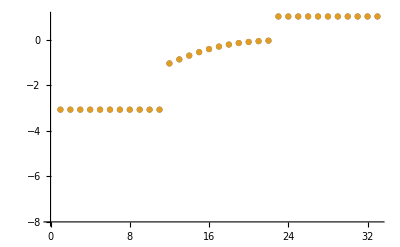

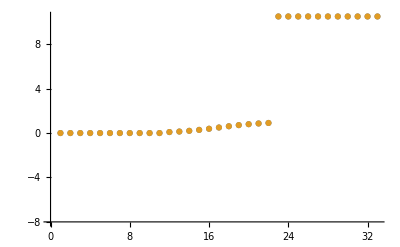

```mathematica
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[1,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[1,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```



```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```



```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```



```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=0.01;
paramSet = 5;
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, absoluteRateForward, absoluteRateReverse, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

data value | predicted value | error in %
0.00017 | 0.00017 | 8.55627×10^-10
0.00019 | 0.00017 | 10.5263
0.00024 | 0.00017 | 29.1667
0.00085 | 0.00017 | 80.

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
10.5 | 10.5 | 7.99479×10^-10
8.17 | 10.5 | 28.519
10.33 | 10.5 | 1.64569

```mathematica
backCalculateRatios[haldaneDataList[[1]][[1]], haldaneDataList[[1]][[2]], paramFitSub]//TableForm
```

data value | predicted value | error in %
0.00085 | 0.00085 | 1.44893×10^-9